```mathematica
vx[t_]:=Sqrt[3t];
vy[t_]:=3Cos[t^2/2];
```

## Version A

```mathematica
initalPosition := {2,4};
accelTime := 4.;
targetSpeed=3.5;
maxTime = 4;
```

### Number 1

```mathematica
{vx'[t],vy'[t]} /. t->accelTime
```

{0.433013,-11.8723}

### Number 2

```mathematica
initialPosition+NIntegrate[{vx[t],vy[t]},{t,4,0}]
```

{-7.2376,0.600604}

### Number 3

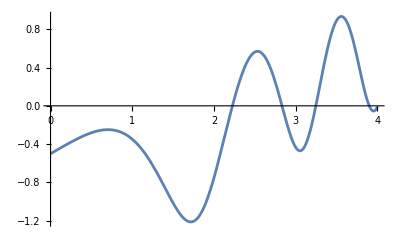

```mathematica
Plot[Sqrt[vx[t]^2+vy[t]^2]-targetSpeed,{t,0,4}]
```

```mathematica
FindRoot[Sqrt[vx[t]^2+vy[t]^2]-targetSpeed,{t,2,2.5}]
```

{t→2.22558}

### Number 4

```mathematica
NIntegrate[Sqrt[vx[t]^2+Sqrt[vy[t]^2]],{t,0,maxTime}]
```

11.1288

## Version B

```mathematica
ClearAll[initialPosition,accelTime,targetSpeed,maxTime]
initialPosition := {2,5};
accelTime := 5.;
targetSpeed=3.2;
maxTime = 5;
```

### Number 1

```mathematica
{vx'[t],vy'[t]} /. t->accelTime
```

{0.387298,0.994828}

### Number 2

```mathematica
initialPosition+NIntegrate[{vx[t],vy[t]},{t,4,0}]
```

{-7.2376,1.6006}

### Number 3

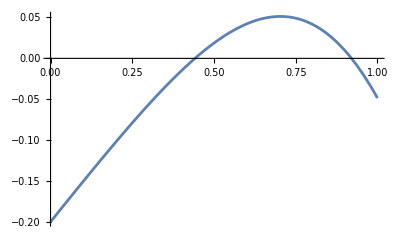

```mathematica
Plot[Sqrt[vx[t]^2+vy[t]^2]-targetSpeed,{t,0,1}]
```

```mathematica
FindRoot[Sqrt[vx[t]^2+vy[t]^2]-targetSpeed,{t,0,0.5}]
```

{t→0.441822}

### Number 4

```mathematica
NIntegrate[Sqrt[vx[t]^2+vy[t]^2],{t,0,maxTime}]
```

17.4168

## Version C

```mathematica
ClearAll[initialPosition,accelTime,targetSpeed,maxTime]
initialPosition := {2,5};
accelTime := 4.;
targetSpeed=3.2;
maxTime = 5;
```

### Number 1

```mathematica
{vx'[t],vy'[t]} /. t->accelTime
```

{0.433013,-11.8723}

### Number 2

```mathematica
initialPosition+NIntegrate[{vx[t],vy[t]},{t,4,1}]
```

{-6.0829,4.52647}

### Number 3

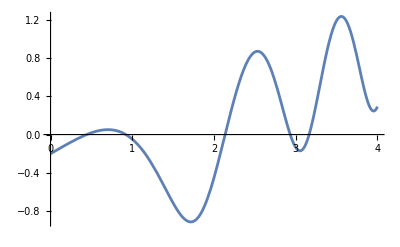

```mathematica
Plot[Sqrt[vx[t]^2+vy[t]^2]-targetSpeed,{t,0,4}]
```

```mathematica
FindRoot[Sqrt[vx[t]^2+vy[t]^2]-targetSpeed,{t,0,0.5}]
```

{t→0.441822}

### Number 4

```mathematica
NIntegrate[Sqrt[vx[t]^2+vy[t]^2],{t,0,5}]
```

17.4168

## Version C

```mathematica
ClearAll[initialPosition,accelTime,targetSpeed,maxTime]
initialPosition := {1,4};
accelTime := 6.;
targetSpeed=3.2;
maxTime = 5;
```

### Number 1

```mathematica
{vx'[t],vy'[t]} /. t->accelTime
```

{0.353553,13.5178}

### Number 2

```mathematica
initialPosition+NIntegrate[{vx[t],vy[t]},{t,4,1}]
```

{-7.0829,3.52647}

### Number 3

```mathematica
Plot[Sqrt[vx[t]^2+vy[t]^2]-targetSpeed,{t,0,4}]
```

-Graphics-

```mathematica
FindRoot[Sqrt[vx[t]^2+vy[t]^2]-targetSpeed,{t,0,0.5}]
```

{t→0.441822}

### Number 4

```mathematica
NIntegrate[Sqrt[vx[t]^2+vy[t]^2],{t,1,4}]
```

10.0099